# OpenTA: Exercise 1.2

#### Consider the dynamical system with for different values of the parameters and . For , the system undergoes a transcritical bifurcation at along the -direction. Define the fixed points of the system by . Remember, Transcritical bifurcation :

```mathematica
f[x_,h_,r_]:= h + x(r-x)
Manipulate[Plot[f[x,10,r],{x,-10,10},AxesLabel -> {"", ""}],{r,-10,10}]
```

Important to notice, if one moves away from , to , and moves on to  something important happens! To understand this set .

An unstable fix point appears at , why is that and why is it unstable?

Well this is because of the function, which for  , corresponds to the specific bifurcation function  which is equal to zero for this settings of r and x.  That it’s unstable can be read off while looking at the y-axis. If y<0 the flow moves to the left and for y>0 it moves to the right. So the fix point at  is stable.

What happens when you move . Well the fix points remain. The unstable remains unstable but changes its position while the stable fix remains unchanged. This holds until you reach . Then the fix unstable fix point vanishes and the fix point at  becomes semi-stable, meaning the flow moves in the same direction, both to the left and right of the fix point (in this case it’s to the left).

Now as  another crucial thing happens, namely the fix point at  becomes unstable and a new stable fix point arises! 

Compared to the saddle-node bifurcation this is a new behaviour, since the fix points do not disappear after the bifurcation, instead they just change stability! 

This change in stability will now be show by a plot in the -plane.

Now we can plot this in -plane by the same mechano used in OpenTA 1.1. For this define the function  since .

```mathematica
f[x_]:= h+x(r-x)
fps=Solve[f[x]==0,x]//Flatten//Simplify
```

{x→1/2 (r-√(4 h+r^2)),x→1/2 (r+√(4 h+r^2))}

```mathematica
D[f[x],x]/.fps[[1]];
D[f[x],x]/.fps[[2]];
```

```mathematica
p1 = Plot[{fps[[1, 2]]}, {r, -1, 0}, PlotStyle -> {Blue}];
p2 = Plot[{fps[[2, 2]]}, {r, -1, 0}, PlotStyle -> {Dashed, Red}];
p3 = Plot[{fps[[2, 2]]}, {r, 0, 1}, PlotStyle -> {Blue}];
p4 = Plot[{fps[[1, 2]]}, {r, 0, 1}, PlotStyle -> {Dashed, Red}];
Show[p1, p2, p3, p4, PlotRange -> All, AxesLabel -> {"", ""}]
```

-Graphics-

What are we looking at all fix points for the function  when r is changed. Due to knowledge from the plot before, it is possible to show which fix points are stable. Also notice the switch from stable to unstable and vice versa!

#### a) Make a plot of the plane. Label different regions according to the number and the types (stable or unstable) of fixed points for in that region. The different regions are separated by a bifurcation curve that you are supposed to draw into your plot. Upload the plot as .pdf or .png.

What I need is the  such that i can plot the (h,r)-plane. Question, how do i get it? Start off by using the tangency condition. We know from the analysis of the function  and the knowledge that h is a constant that where they touch there their slope must be parallel. Since h is a constant, this means it’s slope is going to be 0. That’s what we’ll leverage, so let’s derive with respect to x.

 
Now we look for the intersecting points of h and . 
 becomes  and from this we can get . 
 becomes  and from this we can get

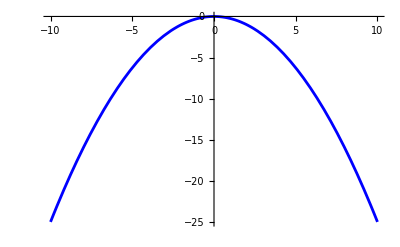

```mathematica
h[r_]:= -r^2/4
p1=Plot[h[r],{r,-10,10}, PlotStyle -> {Blue}];
Show[p1,   PlotRange -> All, AxesLabel -> {"",""}]
```

Comparing this plot with the ()-plot we see that on the line its always an unstable fix point.

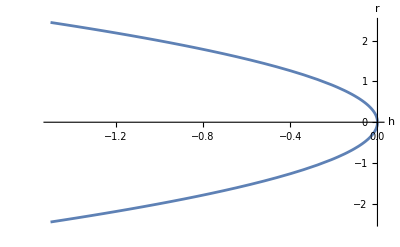

```mathematica
r[h_]:= Sqrt[-4 h]
p1=Plot[r[h],{h,-1.5,1.5}];
p2=Plot[-r[h],{h,-1.5,1.5}];
Show[p1, p2, PlotRange -> All, AxesLabel -> {"h","r"}]
```

#### b) Make a three-dimensional -plot of the surface of fixed points, where . Upload the plot (.pdf or .png).

```mathematica
f[x_, h_, r_] := h + x (r - x)

ContourPlot3D[f[x, h, r] == 0, {x, -10, 10}, {h, -10, 10}, {r, -10, 10}, 
 AxesLabel -> {"x", "h", "r"},
 ViewPoint -> {1, 0, 0},    (* Adjust the viewpoint *)
 ViewVertical -> {0, 1, 0},  (* Adjust the view direction for projection onto rh-plane *)
 ViewCenter -> {0.5, 0.5, 0.5},  (* Set the center of the view *)
 ViewProjection -> "Orthographic"  (* Use orthographic projection *)
]
```

-Graphics3D-

The code above takes the 3D plot and lets us look at the  -plane. Luckily we received the same plot in a).

#### c) Find an analytical expression for the bifurcation curve []. Write your result as a vector that depends on r.

This has been solved for the plot of a).

#### d) At the bifurcation point , a transcritical bifurcation occurs along the r-direction. Similarly, for each point, [], on the bifurcation curve, a transcritical bifurcation occurs in one direction that depends on r. Find this direction analytically. Write your result as a vector in the [h,r]-plane that depends on r. For definiteness, normalise the vector to unity and make sure your solution is equal to [0,1] for h=0.

For this lets take  and derive it with respect to r. This results in , thus the vector looks like  . It remains to normalise this vector to unity. For this calculate , then calculate the .